# Outage-Capacity Bound

## Exponential Distribution X_i~exp(1)

## Basic Calculations

## First Steps

```mathematica
ClearAll[a, n, c, x, f, F, G, H, T, L, R, phi, psi, cmin]
f[x_]:=Exp[-x]
F[x_] := 1-Exp[-x]
G[x_] := -Log[1-x]
```

```mathematica
H[x_, n_, a_]:= (n-1)*G[a+(n-1)x]+G[1-x]
```

```mathematica
T[x_, n_, a_]:=Integrate[H[x, n, a], x]
T[x, n, a]
```

n x-x Log[x]+(1-a+x-n x) Log[1-a+x-n x]

```mathematica
T[x_, n_, a_]:=n x-x Log[x]+(1-a+x-n x) Log[1-a+x-n x]
T[x, n, a]
```

n x-x Log[x]+(1-a+x-n x) Log[1-a+x-n x]

### Left Hand/Right Hand Sides

```mathematica
T[(1-a)/n, n, a]
T[c, n, a]
```

1-a

c n-c Log[c]+(1-a+c-c n) Log[1-a+c-c n]

```mathematica
L[c_, n_, a_]:=(1-a) - (c n-c Log[c]+(1-a+c-c n) Log[1-a+c-c n])
Simplify[(1-a) - (c n-c Log[c]+(1-a+c-c n) Log[1-a+c-c n])]
```

1-a-c n+c Log[c]+(-1+a+c (-1+n)) Log[1-a+c-c n]

```mathematica
R[c_, n_, a_]:= ((1-a)/n-c)H[c, n, a]
```

```mathematica
Simplify[L[c, n, a]>=R[c, n, a], {c≥0, n>2}]
```

(-1+a) Log[1-a+c-c n]≥n (-1+a+c n)+(-1+a) Log[c]

### Determine c_min

```mathematica
(*Reduce[L[c, n, a]≥R[c, n, a],c]*)
Reduce[L[c, 3, 0]≥R[c, 3, 0],c]
```

Root0.0945Root[{-3+Log[1-2 #1]-Log[#1]+9 #1&,0.094541577788104161991}]0.09454157778810417≤c<1/2

```mathematica
Root"0.0945"Root[{-3+Log[1-2 #1]-Log[#1]+9 #1&,0.09454157778810416199097843006298520614`20.599372240690702}]0.09454157778810417≤c<1/2
cmin[n_, a_] := N[Reduce[L[c, n, a]≥R[c, n, a],c][[1]]]
cmin[3, 0]
```

Root0.0945Root[{-3+Log[1-2 #1]-Log[#1]+9 #1&,0.094541577788104161991}]0.09454157778810417≤c<1/2

0.0945416

```mathematica
Manipulate[Reduce[L[c, 3, a]≥R[c, 3, a],c], {a, 0, 1, Appearance->"Labeled"}, ContinuousAction->False] (*Different a*)
```

```mathematica
Manipulate[Reduce[L[c, n, 0]≥R[c, n, 0],c], {n, 2, 10, Appearance->"Labeled", Integer}] (*Different n*)
```

```mathematica
Manipulate[Reduce[L[c, n, a]≥R[c, n, a],c], {n, 2, 10, Appearance->"Labeled", Integer}, {a, 0, 1, Appearance->"Labeled"}, ContinuousAction->False]
```

## Plots for Illustration

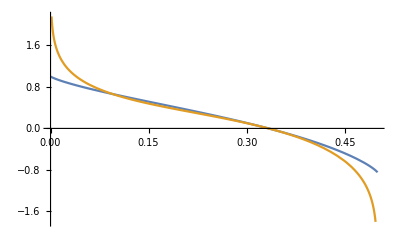

```mathematica
Plot[{L[c, 3, 0],R[c, 3, 0]},{c,0,1/2}]
```

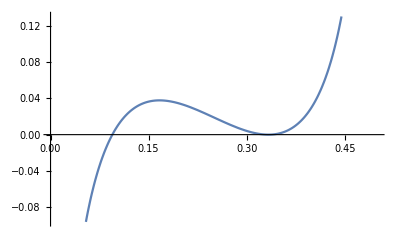

```mathematica
Plot[L[c, 3, 0]-R[c, 3, 0],{c,0,1/2}]
```

```mathematica
Manipulate[Plot[L[c, 3, a]-R[c, 3, a],{c,0,1/2}],{a,0,1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[L[c, n, 0.1]-R[c, n, 0.1],{c,0,1/2}],{n, Range[2,10], Appearance->"Labeled"}]
```

## Calculation of Bounds

## Function ϕ

For a decreasing density the function ϕ is defined according to (3.8) as follows:
	ϕ(a) = Piecewise[{{H(c(a)), if c(a)>0}, {nψ(a), if c(a)=0}}]
with ψ(t)=E[X | X>=G(t)]

```mathematica
psi[a_] := 1/(1-a)*Integrate[x*f[x],{x,G[a],Infinity}]
psi[a]
psi[a_] := ((-1+a) (-1+Log[1-a]))/(1-a)
```

((-1+a) (-1+Log[1-a]))/(1-a)

```mathematica
phi[a_, n_] := Piecewise[{{H[cmin[n, a], n, a], cmin[n, a]>0}, {n*psi[a], cmin[n, a]==0}}]
```

```mathematica
N[phi[0, 3]]
```

2.7779

### Plots

```mathematica
Manipulate[Plot[{H[cmin[n, a], n, a], n*psi[a]},{a,0,1}, PlotLegends->{"H", "nψ"}], {n, 3, 10, Appearance->"Labeled", Integer}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.